```mathematica
Γ=(γu nu+γl nl)/2


NP=(γc γu γl (nl−nu))/(γu γl (3nl nu+nu+nl)+2γc (3Γ+γu+γl))
```

0.277

(7.18123 ϵ^2)/(1.0864+42.3249 ϵ^2)

```mathematica
d=γu γl (3nl nu+nu+nl)+2γc (3Γ+γu+γl)
```

1.0864+42.3249 ϵ^2

```mathematica
CL=(2γc+4Γ+γl+γu)/d
```

```mathematica
(2 γc+γl+γu+2 (nl γl+nu γu))/((nl+nu+3 nl nu) γl γu+2 γc (γl+γu+3/2 (nl γl+nu γu)))
```

(3.208+14.4404 ϵ^2)/(1.0864+42.3249 ϵ^2)

```mathematica
c=CL+(γu γl (3nl nu+nl+nu))/(Γ*d)
```

3.92202/(1.0864+42.3249 ϵ^2)+(3.208+14.4404 ϵ^2)/(1.0864+42.3249 ϵ^2)

1/2 (nl γl+nu γu)

```mathematica
Q[ϵ_]=Log[nl (nu+1)/(nu (nl+1))]*((nl (nu+1)+nu (nl+1))/(nl-nu))-2*NP*c
```

3.68142-(14.3625 ϵ^2 (3.92202/(1.0864+42.3249 ϵ^2)+(3.208+14.4404 ϵ^2)/(1.0864+42.3249 ϵ^2)))/(1.0864+42.3249 ϵ^2)

```mathematica
nl=5
nu=0.027
γu=2
γl=0.1
γc=2(ϵ)^2/Γ
```

5

0.027

2

0.1

7.22022 ϵ^2

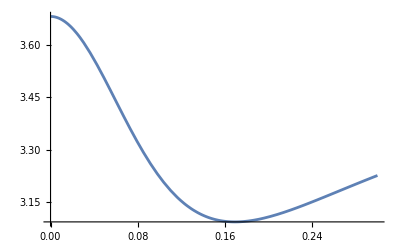

```mathematica
Plot[Q[ϵ],{ϵ,0,0.3}]
```